```mathematica
SetDirectory[NotebookDirectory[]];
<<"tools5314.wl"
<<"mainfuncs1.m"
```

#### Numerical substitution rules:

```mathematica
trigrep[i_]:={Cos[ToExpression[Symbol[ToString[α]<>ToString[i]]]]-> ToExpression[Symbol[ToString[lambda]<>ToString[i]]],Sin[ToExpression[Symbol[ToString[α]<>ToString[i]]]]-> ToExpression[Symbol[ToString[mu]<>ToString[i]]],Sec[ToExpression[Symbol[ToString[α]<>ToString[i]]]]-> 1/(ToExpression[Symbol[ToString[lambda]<>ToString[i]]]),Csc[ToExpression[Symbol[ToString[α]<>ToString[i]]]]-> 1/(ToExpression[Symbol[ToString[mu]<>ToString[i]]]),Tan[ToExpression[Symbol[ToString[α]<>ToString[i]]]]-> ((ToExpression[Symbol[ToString[mu]<>ToString[i]]])/(ToExpression[Symbol[ToString[lambda]<>ToString[i]]])),Cot[ToExpression[Symbol[ToString[α]<>ToString[i]]]]-> ((ToExpression[Symbol[ToString[lambda]<>ToString[i]]])/(ToExpression[Symbol[ToString[mu]<>ToString[i]]]))};
alpharep[i_]:={ToExpression[Symbol[ToString[α]<>ToString[i]]]-> ToExpression[Symbol[ToString[alpha]<>ToString[i]]]};
alpharepall=Union[alpharep[1],alpharep[2],alpharep[3],alpharep[4],alpharep[5],alpharep[6]];
revtrigrep[i_]:=Reverse[trigrep[i],2];
trigrepall=Union[trigrep[1],trigrep[2],trigrep[3],trigrep[4],trigrep[5],trigrep[6]];
revtrigrepall=Union[revtrigrep[1],revtrigrep[2],revtrigrep[3],revtrigrep[4],revtrigrep[5],revtrigrep[6]];
replist=Union[{Power-> pow},trigrepall,{Sin[x_]-> sin[x]},{Cos[x_]-> cos[x]},{Tan[x_]-> tan[x]},{Csc[x_]-> 1/sin[x]},{Sec[x_]-> 1/cos[x]},{Cot[x_]->sin[x]/cos[x]} ];
revreplist=Reverse[replist,2];
revalpharepall=Reverse[alpharepall,2];
inversetrig =  Union[{ArcTan[x_, y_]->atan2[y,x]} , {ArcCos[x_]->acos[x]}];
```

```mathematica
b1 = {0, 0};
b2 = {l0, 0};
p1 = b1+{l1 Cos[θ1], l1 Sin[θ1]};
p2 = b2+{l1 Cos[θ2], l1 Sin[θ2]};
```

```mathematica
η1 = p1+{r1 Cos[ϕ1], r1 Sin[ϕ1]}-{x, y};
η2 = p2+{r1 Cos[ϕ2], r1 Sin[ϕ2]}-{x, y};
```

```mathematica
eq1 = Simplify[Expand[(Cos[θ1]^2+Sin[θ1]^2-1)/.Solve[η1==0, {Cos[θ1], Sin[θ1]}]][[1]]];
```

```mathematica
eq2= Simplify[Expand[(Cos[θ2]^2+Sin[θ2]^2-1)/.Solve[η2==0, {Cos[θ2], Sin[θ2]}]][[1]]];
```

```mathematica
(*Cases of singularity is Sin[ϕ1-ϕ2]=0, i.e. ϕ1 = ϕ2 or ϕ2 = π + ϕ1 *)
```

```mathematica
eq3 = Factor[Simplify[Expand[(Cos[ϕ1]^2+Sin[ϕ1]^2-1)/.Solve[{(eq2/.{ϕ2->π+ϕ1})==0, eq1==0}, {Cos[ϕ1], Sin[ϕ1]}]][[1]]]][[5]]
```

l0^2 l1^4-2 l0^2 l1^2 r1^2+l0^2 r1^4+2 l0^3 l1^2 x-4 l0 l1^4 x-2 l0^3 r1^2 x+8 l0 l1^2 r1^2 x-4 l0 r1^4 x+l0^4 x^2-10 l0^2 l1^2 x^2+4 l1^4 x^2+10 l0^2 r1^2 x^2-8 l1^2 r1^2 x^2+4 r1^4 x^2-6 l0^3 x^3+16 l0 l1^2 x^3-16 l0 r1^2 x^3+13 l0^2 x^4-8 l1^2 x^4+8 r1^2 x^4-12 l0 x^5+4 x^6+l0^4 y^2-6 l0^2 l1^2 y^2+4 l1^4 y^2+2 l0^2 r1^2 y^2-8 l1^2 r1^2 y^2+4 r1^4 y^2-6 l0^3 x y^2+16 l0 l1^2 x y^2-16 l0 r1^2 x y^2+18 l0^2 x^2 y^2-16 l1^2 x^2 y^2+16 r1^2 x^2 y^2-24 l0 x^3 y^2+12 x^4 y^2+5 l0^2 y^4-8 l1^2 y^4+8 r1^2 y^4-12 l0 x y^4+12 x^2 y^4+4 y^6

```mathematica
(*Verifying the circularity*)
```

```mathematica
Simplify[Factor[Simplify[eq3/.{x->X/w, y->Y/w}]][[2]]/.w->0]
```

4 (X^2+Y^2)^3

```mathematica
(*Cases of singularity is Sin[ϕ1-ϕ2]=0, i.e. ϕ1 = ϕ2 or ϕ2 = π + ϕ1 *)
```

```mathematica
eq4 = Factor[Simplify[Expand[(Cos[ϕ1]^2+Sin[ϕ1]^2-1)/.Solve[{(eq2/.{ϕ2->ϕ1})==0, eq1==0}, {Cos[ϕ1], Sin[ϕ1]}]][[1]]]][[4]]
```

l1^4-2 l1^2 r1^2+r1^4-2 l0 l1^2 x+2 l0 r1^2 x+l0^2 x^2+2 l1^2 x^2-2 r1^2 x^2-2 l0 x^3+x^4+l0^2 y^2-2 l1^2 y^2-2 r1^2 y^2-2 l0 x y^2+2 x^2 y^2+y^4

```mathematica
(*Verifying the circularity*)
```

```mathematica
Simplify[Factor[Simplify[eq4/.{x->X/w, y->Y/w}]][[2]]/.w->0]
```

(X^2+Y^2)^2

```mathematica
Simplify[Coefficient[Factor[Together[Simplify[eq4/.{x->X/w, y->Y/w}]]][[2]],w^2]]
```

2 l1^2 (X^2-Y^2)+l0^2 (X^2+Y^2)-2 r1^2 (X^2+Y^2)

```mathematica
(*largest radius problem with the first case*)
```

```mathematica
cir = (x-h)^2+(y-k)^2-r^2
```

-r^2+(-h+x)^2+(-k+y)^2

```mathematica
(*Making the cross of their respective gradients zero*)
```

```mathematica
tc1 = Factor[Det[D[{eq3, cir}, {{x, y}}]]][[2]]
```

k l0^3 l1^2-2 k l0 l1^4-k l0^3 r1^2+4 k l0 l1^2 r1^2-2 k l0 r1^4+k l0^4 x-10 k l0^2 l1^2 x+4 k l1^4 x+10 k l0^2 r1^2 x-8 k l1^2 r1^2 x+4 k r1^4 x-9 k l0^3 x^2+24 k l0 l1^2 x^2-24 k l0 r1^2 x^2+26 k l0^2 x^3-16 k l1^2 x^3+16 k r1^2 x^3-30 k l0 x^4+12 k x^5-h l0^4 y+6 h l0^2 l1^2 y-l0^3 l1^2 y-4 h l1^4 y+2 l0 l1^4 y-2 h l0^2 r1^2 y+l0^3 r1^2 y+8 h l1^2 r1^2 y-4 l0 l1^2 r1^2 y-4 h r1^4 y+2 l0 r1^4 y+6 h l0^3 x y-16 h l0 l1^2 x y+4 l0^2 l1^2 x y+16 h l0 r1^2 x y-8 l0^2 r1^2 x y-18 h l0^2 x^2 y+3 l0^3 x^2 y+16 h l1^2 x^2 y-8 l0 l1^2 x^2 y-16 h r1^2 x^2 y+8 l0 r1^2 x^2 y+24 h l0 x^3 y-8 l0^2 x^3 y-12 h x^4 y+6 l0 x^4 y-3 k l0^3 y^2+8 k l0 l1^2 y^2-8 k l0 r1^2 y^2+18 k l0^2 x y^2-16 k l1^2 x y^2+16 k r1^2 x y^2-36 k l0 x^2 y^2+24 k x^3 y^2-10 h l0^2 y^3+3 l0^3 y^3+16 h l1^2 y^3-8 l0 l1^2 y^3-16 h r1^2 y^3+8 l0 r1^2 y^3+24 h l0 x y^3-8 l0^2 x y^3-24 h x^2 y^3+12 l0 x^2 y^3-6 k l0 y^4+12 k x y^4-12 h y^5+6 l0 y^5

```mathematica
monopoly[tc1/.h->l0/2, {y}][[2]]
```

{1,y,y^2,y^3,y^4}

```mathematica
Export["eq3.txt", CForm[FullSimplify[eq3/.h->l0/2]/.replist]]
```

eq3.txt

```mathematica
eq3/.sample2/.x->-1/.y->0
```

0

```mathematica
Export["coefftc12.txt", Simplify[monopoly[Simplify[tc1/.h->l0/2], {y}]][[1]]/.replist]
```

coefftc12.txt

```mathematica
(*This is a bicircular pentic*)
```

```mathematica
Simplify[Numerator[Simplify[tc1/.{x->X/w, y->Y/w}]]/.w->0]
```

6 (2 k X+(-2 h+l0) Y) (X^2+Y^2)^2

```mathematica
(*Solving the equations of the singulartiy curve and the pentic*)
```

```mathematica
sy1 = ResidualSylv[tc1, eq3, y][[1]]/.h->l0/2;
```

```mathematica
(*imposing symmetry and factorizing the equations*)
```

```mathematica
Variables[sy1]
```

{l0,l1,r1,x,k}

```mathematica
sample = {l0->1.5, l1->1, r1->3/4, k->1.5}
```

{l0→1.5,l1→1,r1→3/4,k→1.5}

```mathematica
sy1f = Simplify[Factor[sy1/.h->l0/2]];
```

```mathematica
Variables[sy1f[[5]]]
```

{l0,l1,r1,x,k}

```mathematica
xcoeff = Simplify[monopoly[sy1f[[5]], {x}][[1]]];
```

```mathematica
Export["xcoeff.txt", CForm[xcoeff/.replist]]
```

xcoeff.txt

```mathematica
sample
```

{l0→1.5,l1→1,r1→3/4,k→1.5}

```mathematica
sample2 = {l0->2, l1->2, r1->1, k->1.5}
```

{l0→2,l1→2,r1→1,k→1.5}

```mathematica
Solve[(sy1f[[5]]/.sample2)==0, x]
```

{{x→-1.},{x→-1.},{x→-0.5547},{x→0.5547},{x→1.4453},{x→2.5547},{x→3.},{x→3.}}

```mathematica
Directory[]
```

/home/akhil/Akhil/fivebar/Five Bar Design

```mathematica
Export["ycoeff.txt", CForm[FullSimplify[monopoly[tc1/.h->l0/2, {y}][[1]]]/.replist]]
```

ycoeff.txt

```mathematica
Solve[(tc1/.h->l0/2/.sample2/.x->-1)==0, y]
```

{{y→-0.444444-1.94999 ⅈ},{y→-0.444444+1.94999 ⅈ},{y→0.},{y→0.}}

```mathematica
Export["yeqn.txt", CForm[monopoly[Simplify[tc1/.h->l0/2],{y}][[1]]/.replist]]
```

yeqn.txt

```mathematica
monopoly[Simplify[tc1/.h->l0/2],{y}][[2]]
```

{1,y,y^2,y^3,y^4}

```mathematica
(*This is how we need to solve for y but this takes a lot of computational time*)
```

```mathematica
(*tc1h = tc1/.h->l0/2;
ex1 = Simplify[PolynomialRemainder[eq3, tc1h, y]];
ex2 = Simplify[PolynomialRemainder[tc1h, ex1,y]];
ex3 = PolynomialRemainder[ex1, ex2,y];
ex4 = CForm[ex3/.replist];
Export["ex4.txt", ex4]
"ex4.txt"*)
```

```mathematica
(*6 degree factoring out*)
```

```mathematica
sy1f[[3]]
```

(l0-2 x)^6

```mathematica
(*4 degree factoring out*)
```

```mathematica
sy1f[[4]]
```

(l1^2-r1^2+(l0-x) x)^2

```mathematica
sy1f[[5]];
```

```mathematica
sc3x = Solve[Factor[sy1f[[3]]][[1]]==0, x][[1]]
```

{x→l0/2}

```mathematica
(*Now solving for y*)
```

```mathematica
tr1 = Simplify[eq3/.sc3x];
```

```mathematica
(*One solution is y being equal to 0*)
```

```mathematica
sc3y = Solve[tr1==0, y];
```

```mathematica
sc3yd = Simplify[DeleteDuplicates[sc3y]]
```

{{y→0},{y→-1/2 √(-l0^2+4 l1^2-4 l0 r1-4 r1^2)},{y→1/2 √(-l0^2+4 l1^2-4 l0 r1-4 r1^2)},{y→-1/2 √(-l0^2+4 l1^2+4 l0 r1-4 r1^2)},{y→1/2 √(-l0^2+4 l1^2+4 l0 r1-4 r1^2)}}

```mathematica
(*The solution for this is x = l0/2 and it repeats 6 times*)
```

```mathematica
sc2x = Solve[Factor[sy1f[[4]]][[1]]==0, x]
```

{{x→1/2 (l0-√(l0^2+4 l1^2-4 r1^2))},{x→1/2 (l0+√(l0^2+4 l1^2-4 r1^2))}}

```mathematica
tr2 = Simplify[eq3/.sc2x];
```

```mathematica
(*y=0 is one solution*)
```

```mathematica
sc2y = Simplify[Solve[tr2==0, y]];
```

```mathematica
sc2yd = Simplify[DeleteDuplicates[sc2y]]
```

{{y→0},{y→-(√(-5 l0^2-4 l1^2+4 r1^2-√(9 l0^4+16 (l1^2-r1^2)^2+8 l0^2 (5 l1^2+3 r1^2))))/(2 √2)},{y→(√(-5 l0^2-4 l1^2+4 r1^2-√(9 l0^4+16 (l1^2-r1^2)^2+8 l0^2 (5 l1^2+3 r1^2))))/(2 √2)},{y→-(√(-5 l0^2-4 l1^2+4 r1^2+√(9 l0^4+16 (l1^2-r1^2)^2+8 l0^2 (5 l1^2+3 r1^2))))/(2 √2)},{y→√(-(5 l0^2)/8+1/8 (-4 l1^2+4 r1^2+√(9 l0^4+16 (l1^2-r1^2)^2+8 l0^2 (5 l1^2+3 r1^2))))}}

```mathematica
sol1 = DeleteDuplicates[ArrayReshape[Flatten[DeleteDuplicates[Outer[List, sc3x, sc3y]]//.{x_List}:>x],{6, 2}]];
```

```mathematica
(*Now verifying the same for the other set of curves*)
```

```mathematica
sol2  = DeleteDuplicates[ArrayReshape[Flatten[DeleteDuplicates[Outer[List, sc2x, sc2y]]//.{x_List}:>x],{12, 2}]];
```

```mathematica
sols = Union[sol1, sol2];
sy1sols=sols;
```

```mathematica
sols//Dimensions
```

{15,2}

```mathematica
(*And the remaining factor is in its 8th order and needs to be solved numerically*)
```

```mathematica
(*Solve[sy1f[[5]]==0, x]*)
```

```mathematica
(*Now along with these solutions we need to solve the 8th order non-linear equation to get the other solutions in x, *)
```

```mathematica
(*Solve[(sy1f[[5]])==0, x]*) (*It dumped the core!*)
```

```mathematica
(*And then substitute this solution into eq3 and find the corresponding solutions of y *)
```

```mathematica
(*Investigating the solutions in a sample case by plotting the curves*)
```

```mathematica
(*Show[ContourPlot[(eq4/.sample)==0, {x, -2, 2}, {y, -2, 2}, PlotPoints->250], ContourPlot[(eq3/.sample)==0, {x, -2, 2}, {y, -2, 2}, PlotPoints->250]]*)
```

```mathematica
(*Verifying that the eq4 is just the circles of FSM and hecne finding the roots is simple*)
```

```mathematica
Expand[(Expand[(y-Sqrt[l1^2-(l0/2)^2])^2+(x-l0/2)^2-r1^2])*(Expand[(y+Sqrt[l1^2-(l0/2)^2])^2+(x-l0/2)^2-r1^2])]
```

l1^4-2 l1^2 r1^2+r1^4-2 l0 l1^2 x+2 l0 r1^2 x+l0^2 x^2+2 l1^2 x^2-2 r1^2 x^2-2 l0 x^3+x^4+l0^2 y^2-2 l1^2 y^2-2 r1^2 y^2-2 l0 x y^2+2 x^2 y^2+y^4

```mathematica
(*Going through the same procedure for finding radius with FSM circles*)
```

```mathematica
tc2 = Factor[Det[D[{eq4, cir}, {{x, y}}]]][[2]];
```

```mathematica
sy2 = Factor[Simplify[ResidualSylv[tc2, eq4, y][[1]]/.h->l0/2]];
```

```mathematica
(*Now getting these solutions*)
```

```mathematica
sy2x1 = Solve[sy2[[5]][[1]]==0, x][[1]];
```

```mathematica
sy2y1 = DeleteDuplicates[Simplify[Solve[Simplify[eq4/.sy2x1]==0, y]]];
```

```mathematica
sy2x2 = Solve[sy2[[6]][[1]]==0, x];
```

```mathematica
sy2y2 = DeleteDuplicates[Simplify[Solve[Simplify[eq4/.sy2x2]==0, y]]];
```

```mathematica
sy2sol1 = Outer[List, sy2x1, sy2y1]//.{x_List}:>x;
sy2sol2 = ArrayReshape[(Outer[List, sy2x2, sy2y2]//.{x_List}:>x),{6, 2}];
sy2sols = DeleteDuplicates[Join[sy2sol1, sy2sol2]]//.{x_List}:>x;
```

```mathematica
Dimensions[sy2sols]
```

{10,2}

```mathematica
allsols =DeleteDuplicates[Union[sy1sols, sy2sols]];
```

```mathematica
rad= Simplify[√(x^2+(y-k)^2)/.allsols];
```

```mathematica
rad//Dimensions
```

{25}

```mathematica
rad/.sample
```

{1.67705,1.75671,3.00649,1.59833,0.755211,1.62214+1.03385 ⅈ,1.62214-1.03385 ⅈ,2.61008,0.901388,1.52069,1.50856+1.79255 ⅈ,1.50856-1.79255 ⅈ,1.52069,1.52069,2.30489,1.98126+1.36487 ⅈ,1.98126-1.36487 ⅈ,2.30489,2.30489,1.55151,2.85058,0.434215,1.86221,3.03092,1.11768}

```mathematica
Export["rads.txt", CForm[rad/.replist]]
```

rads.txt

```mathematica
(*We can simply find the radius of such a curve*)
```

```mathematica
fsmc1 = {l0/2, Sqrt[l1^2-(l0/2)^2]};
fsmc2 = {l0/2, -Sqrt[l1^2-(l0/2)^2]};
pc = {h, k};
```

```mathematica
computed[d_, pc_]:= Module[{},Sqrt[(d-pc).(d-pc)]]
```

```mathematica
(*Once we compute computed[fsmc1, pc], if that is greater than the radius of the circle then computed-r1, computed+r1, shall be the radii, else, r1-computed and r1+computed shall be the roots*)
```

```mathematica
(*each of the x's gives rise to each of the y's*)
```

```mathematica
Solve[(sy1f[[5]]/.sample)==0, x]
```

{{x→-0.25},{x→-0.25},{x→-0.0466919},{x→0.316982},{x→1.18302},{x→1.54669},{x→1.75},{x→1.75}}

```mathematica
temp = Simplify[eq3/.Solve[(sy1f[[5]]/.sample)==0, x]/.sample]
```

{0.+13. y^4+4 y^6,0.+13. y^4+4 y^6,0.338764-4.60862 y^2+8.61661 y^4+4 y^6,0.495123-5.89064 y^2+3.25005 y^4+4 y^6,0.495123-5.89064 y^2+3.25005 y^4+4 y^6,0.338764-4.60862 y^2+8.61661 y^4+4 y^6,-7.10543×10^-15+2.78533×10^-12 y^2+13. y^4+4 y^6,-7.10543×10^-15+2.78533×10^-12 y^2+13. y^4+4 y^6}

```mathematica
Solve[temp[[1]]==0, y]
```

{{y→0.},{y→0.},{y→0.},{y→0.},{y→0.+1.80278 ⅈ},{y→0.-1.80278 ⅈ}}

```mathematica
Solve[temp[[2]]==0, y]
```

{{y→0.},{y→0.},{y→0.},{y→0.},{y→0.+1.80278 ⅈ},{y→0.-1.80278 ⅈ}}

```mathematica
Solve[temp[[3]]==0, y]
```

{{y→-0.604386},{y→-0.298142},{y→0.-1.61503 ⅈ},{y→0.+1.61503 ⅈ},{y→0.298142},{y→0.604386}}

```mathematica
Select[y/.Solve[temp[[3]]==0, y], Im[#]==0&]
```

{-0.604386,-0.298142,0.298142,0.604386}

```mathematica
Solve[temp[[4]]==0, y]
```

{{y→-0.901385},{y→-0.298142},{y→0.-1.30916 ⅈ},{y→0.+1.30916 ⅈ},{y→0.298142},{y→0.901385}}

```mathematica
Select[y/.Solve[temp[[4]]==0, y], Im[#]==0&]
```

{-0.901385,-0.298142,0.298142,0.901385}

```mathematica
Solve[temp[[5]]==0, y]
```

{{y→-0.901385},{y→-0.298142},{y→0.-1.30916 ⅈ},{y→0.+1.30916 ⅈ},{y→0.298142},{y→0.901385}}

```mathematica
Select[y/.Solve[temp[[5]]==0, y], Im[#]==0&]
```

{-0.901385,-0.298142,0.298142,0.901385}

```mathematica
Solve[temp[[7]]==0, y]
```

{{y→-0.000152901},{y→0.-0.000152902 ⅈ},{y→0.+0.000152902 ⅈ},{y→0.-1.80278 ⅈ},{y→0.+1.80278 ⅈ},{y→0.000152901}}

```mathematica
Select[y/.Solve[temp[[7]]==0, y], Im[#]==0&]
```

{-0.000152901,0.000152901}

```mathematica
Solve[temp[[8]]==0, y]
```

{{y→-0.000152901},{y→0.-0.000152902 ⅈ},{y→0.+0.000152902 ⅈ},{y→0.-1.80278 ⅈ},{y→0.+1.80278 ⅈ},{y→0.000152901}}

```mathematica
Select[y/.Solve[temp[[1]]==0, y], Im[#]==0&]
```

{0.,0.,0.,0.}

```mathematica
(*Illustration of the del's becoming zero at a crunode*)
```

```mathematica
D[eq3, x]/.sample/.{x->1.75, y->0}
```

0.

```mathematica
D[eq3, y]/.sample/.{x->1.75, y->0}
```

0.

So to select the largest safe working zone, we need to maximize the smallest radius possible. But in the choice of a smallest radius problem, one might select the acnode of the curve. So once the selection of the point is done one needs to check if the point is valid tangency point or an acnode. So check the D[eq3, x] and D[eq3, y] and if this goes to zero it implies that the point is a double root and can be an acnode or a crunode. But from "expreience" (Aravind's) one can say that a crunode wont give the smallest possible circle. So one can conclude that the point encountered is an acnode. Hence reject that point and move on to select the next smaller radius and do the check and so on until we find the suitable circle. All the solutions we have are,

The derivative was taken just to illustrate the fact that a double root also results in a zero of the det or is an obvious solution to the problem and hence needs to be eliminated. So once we get a solution we need to check if it is double root, if such a solution is chosen for minimum radius.

```mathematica
(*Now getting the radii for the workspace boundaries also*)
```

```mathematica
Wsc1o = {0, 0};
Wsc1i = {0, 0};
Wsc2i = {l0, 0};
Wsc2o = {l0, 0};
```

```mathematica
rinner = computed[Wsc1o, pc]-Abs[l1-r1];
router = (l1+r1) - computed[Wsc1o, pc];
```

```mathematica
Export["wsc12pc.txt",CForm[computed[Wsc1o, pc]/.replist]]
```

wsc12pc.txt

```mathematica
Export["wsc22pc.txt",CForm[computed[Wsc2o, pc]/.replist]]
```

wsc22pc.txt

```mathematica
Export["polycoeffs.txt", CForm[monopoly[sy1f[[5]], {x}][[1]]/.replist]]
```

polycoeffs.txt

```mathematica
Export["coeffsfory.txt", CForm[CoefficientList[eq3, y]/.replist]]
```

coeffsfory.txt

```mathematica
(*Verifying if the solutions from mathematica with the ones on GSL saved in sols from gsl file*)
```

```mathematica
(*We have 8 solutions for that univariate*)
```

```mathematica
Solve[(eq3/.x->0.6/.sample)==0, y]
```

{{y→-0.988686},{y→-0.129486},{y→0.-1.14532 ⅈ},{y→0.+1.14532 ⅈ},{y→0.129486},{y→0.988686}}

```mathematica
NSolve[(sy1f[[5]]/.sample)==0, x]
```

{{x→-0.25},{x→-0.25},{x→-0.0466919},{x→0.316982},{x→1.18302},{x→1.54669},{x→1.75},{x→1.75}}

```mathematica
(*Verified the whole code on 09-07-2018*)
```

```mathematica
(*Now deriving a condition for double points being crunode, acnode or a cusp. Since Dx, Dy dont differentiate between the double points we need to formulate a different way to identify them*)
```

```mathematica
Simplify[Numerator[Together[eq3/.{x->X/w, y->y/w}]]/.{w->0}]
```

4 (X^2+y^2)^3

```mathematica
(*Assume a line passing though the point {p, q} having an equation of y = mx + c, c = q-mp*)
```

```mathematica
monopoly[eq3,{y}]
```

{{l0^2 l1^4-2 l0^2 l1^2 r1^2+l0^2 r1^4+2 l0^3 l1^2 x-4 l0 l1^4 x-2 l0^3 r1^2 x+8 l0 l1^2 r1^2 x-4 l0 r1^4 x+l0^4 x^2-10 l0^2 l1^2 x^2+4 l1^4 x^2+10 l0^2 r1^2 x^2-8 l1^2 r1^2 x^2+4 r1^4 x^2-6 l0^3 x^3+16 l0 l1^2 x^3-16 l0 r1^2 x^3+13 l0^2 x^4-8 l1^2 x^4+8 r1^2 x^4-12 l0 x^5+4 x^6,l0^4-6 l0^2 l1^2+4 l1^4+2 l0^2 r1^2-8 l1^2 r1^2+4 r1^4-6 l0^3 x+16 l0 l1^2 x-16 l0 r1^2 x+18 l0^2 x^2-16 l1^2 x^2+16 r1^2 x^2-24 l0 x^3+12 x^4,5 l0^2-8 l1^2+8 r1^2-12 l0 x+12 x^2,4},{1,y^2,y^4,y^6}}

```mathematica
(*y coefficient is zero*)
```

```mathematica
monomiallist = MonomialList[eq3, {x, y}, "NegativeDegreeReverseLexicographic"]
```

{l0^2 l1^4-2 l0^2 l1^2 r1^2+l0^2 r1^4,(2 l0^3 l1^2-4 l0 l1^4-2 l0^3 r1^2+8 l0 l1^2 r1^2-4 l0 r1^4) x,(l0^4-10 l0^2 l1^2+4 l1^4+10 l0^2 r1^2-8 l1^2 r1^2+4 r1^4) x^2,(l0^4-6 l0^2 l1^2+4 l1^4+2 l0^2 r1^2-8 l1^2 r1^2+4 r1^4) y^2,(-6 l0^3+16 l0 l1^2-16 l0 r1^2) x^3,(-6 l0^3+16 l0 l1^2-16 l0 r1^2) x y^2,(13 l0^2-8 l1^2+8 r1^2) x^4,(18 l0^2-16 l1^2+16 r1^2) x^2 y^2,(5 l0^2-8 l1^2+8 r1^2) y^4,-12 l0 x^5,-24 l0 x^3 y^2,-12 l0 x y^4,4 x^6,12 x^4 y^2,12 x^2 y^4,4 y^6}

```mathematica
(*To find out the double point tangency at a desired point (p, q) we shift the origin to p, q making the coords x->p, y->q*)
```

```mathematica
eq3tr = Expand[eq3/.{x->X+p, y->Y+q}]
```

l0^2 l1^4+2 l0^3 l1^2 p-4 l0 l1^4 p+l0^4 p^2-10 l0^2 l1^2 p^2+4 l1^4 p^2-6 l0^3 p^3+16 l0 l1^2 p^3+13 l0^2 p^4-8 l1^2 p^4-12 l0 p^5+4 p^6+l0^4 q^2-6 l0^2 l1^2 q^2+4 l1^4 q^2-6 l0^3 p q^2+16 l0 l1^2 p q^2+18 l0^2 p^2 q^2-16 l1^2 p^2 q^2-24 l0 p^3 q^2+12 p^4 q^2+5 l0^2 q^4-8 l1^2 q^4-12 l0 p q^4+12 p^2 q^4+4 q^6-2 l0^2 l1^2 r1^2-2 l0^3 p r1^2+8 l0 l1^2 p r1^2+10 l0^2 p^2 r1^2-8 l1^2 p^2 r1^2-16 l0 p^3 r1^2+8 p^4 r1^2+2 l0^2 q^2 r1^2-8 l1^2 q^2 r1^2-16 l0 p q^2 r1^2+16 p^2 q^2 r1^2+8 q^4 r1^2+l0^2 r1^4-4 l0 p r1^4+4 p^2 r1^4+4 q^2 r1^4+2 l0^3 l1^2 X-4 l0 l1^4 X+2 l0^4 p X-20 l0^2 l1^2 p X+8 l1^4 p X-18 l0^3 p^2 X+48 l0 l1^2 p^2 X+52 l0^2 p^3 X-32 l1^2 p^3 X-60 l0 p^4 X+24 p^5 X-6 l0^3 q^2 X+16 l0 l1^2 q^2 X+36 l0^2 p q^2 X-32 l1^2 p q^2 X-72 l0 p^2 q^2 X+48 p^3 q^2 X-12 l0 q^4 X+24 p q^4 X-2 l0^3 r1^2 X+8 l0 l1^2 r1^2 X+20 l0^2 p r1^2 X-16 l1^2 p r1^2 X-48 l0 p^2 r1^2 X+32 p^3 r1^2 X-16 l0 q^2 r1^2 X+32 p q^2 r1^2 X-4 l0 r1^4 X+8 p r1^4 X+l0^4 X^2-10 l0^2 l1^2 X^2+4 l1^4 X^2-18 l0^3 p X^2+48 l0 l1^2 p X^2+78 l0^2 p^2 X^2-48 l1^2 p^2 X^2-120 l0 p^3 X^2+60 p^4 X^2+18 l0^2 q^2 X^2-16 l1^2 q^2 X^2-72 l0 p q^2 X^2+72 p^2 q^2 X^2+12 q^4 X^2+10 l0^2 r1^2 X^2-8 l1^2 r1^2 X^2-48 l0 p r1^2 X^2+48 p^2 r1^2 X^2+16 q^2 r1^2 X^2+4 r1^4 X^2-6 l0^3 X^3+16 l0 l1^2 X^3+52 l0^2 p X^3-32 l1^2 p X^3-120 l0 p^2 X^3+80 p^3 X^3-24 l0 q^2 X^3+48 p q^2 X^3-16 l0 r1^2 X^3+32 p r1^2 X^3+13 l0^2 X^4-8 l1^2 X^4-60 l0 p X^4+60 p^2 X^4+12 q^2 X^4+8 r1^2 X^4-12 l0 X^5+24 p X^5+4 X^6+2 l0^4 q Y-12 l0^2 l1^2 q Y+8 l1^4 q Y-12 l0^3 p q Y+32 l0 l1^2 p q Y+36 l0^2 p^2 q Y-32 l1^2 p^2 q Y-48 l0 p^3 q Y+24 p^4 q Y+20 l0^2 q^3 Y-32 l1^2 q^3 Y-48 l0 p q^3 Y+48 p^2 q^3 Y+24 q^5 Y+4 l0^2 q r1^2 Y-16 l1^2 q r1^2 Y-32 l0 p q r1^2 Y+32 p^2 q r1^2 Y+32 q^3 r1^2 Y+8 q r1^4 Y-12 l0^3 q X Y+32 l0 l1^2 q X Y+72 l0^2 p q X Y-64 l1^2 p q X Y-144 l0 p^2 q X Y+96 p^3 q X Y-48 l0 q^3 X Y+96 p q^3 X Y-32 l0 q r1^2 X Y+64 p q r1^2 X Y+36 l0^2 q X^2 Y-32 l1^2 q X^2 Y-144 l0 p q X^2 Y+144 p^2 q X^2 Y+48 q^3 X^2 Y+32 q r1^2 X^2 Y-48 l0 q X^3 Y+96 p q X^3 Y+24 q X^4 Y+l0^4 Y^2-6 l0^2 l1^2 Y^2+4 l1^4 Y^2-6 l0^3 p Y^2+16 l0 l1^2 p Y^2+18 l0^2 p^2 Y^2-16 l1^2 p^2 Y^2-24 l0 p^3 Y^2+12 p^4 Y^2+30 l0^2 q^2 Y^2-48 l1^2 q^2 Y^2-72 l0 p q^2 Y^2+72 p^2 q^2 Y^2+60 q^4 Y^2+2 l0^2 r1^2 Y^2-8 l1^2 r1^2 Y^2-16 l0 p r1^2 Y^2+16 p^2 r1^2 Y^2+48 q^2 r1^2 Y^2+4 r1^4 Y^2-6 l0^3 X Y^2+16 l0 l1^2 X Y^2+36 l0^2 p X Y^2-32 l1^2 p X Y^2-72 l0 p^2 X Y^2+48 p^3 X Y^2-72 l0 q^2 X Y^2+144 p q^2 X Y^2-16 l0 r1^2 X Y^2+32 p r1^2 X Y^2+18 l0^2 X^2 Y^2-16 l1^2 X^2 Y^2-72 l0 p X^2 Y^2+72 p^2 X^2 Y^2+72 q^2 X^2 Y^2+16 r1^2 X^2 Y^2-24 l0 X^3 Y^2+48 p X^3 Y^2+12 X^4 Y^2+20 l0^2 q Y^3-32 l1^2 q Y^3-48 l0 p q Y^3+48 p^2 q Y^3+80 q^3 Y^3+32 q r1^2 Y^3-48 l0 q X Y^3+96 p q X Y^3+48 q X^2 Y^3+5 l0^2 Y^4-8 l1^2 Y^4-12 l0 p Y^4+12 p^2 Y^4+60 q^2 Y^4+8 r1^2 Y^4-12 l0 X Y^4+24 p X Y^4+12 X^2 Y^4+24 q Y^5+4 Y^6

```mathematica
(*Now my line equation can be y = m*x*)
```

```mathematica
deg2coeff = Numerator[Together[Coefficient[(eq3tr/.Y->m*X),X^2]/.m->X/Y]]
```

l0^4 X^2-6 l0^2 l1^2 X^2+4 l1^4 X^2-6 l0^3 p X^2+16 l0 l1^2 p X^2+18 l0^2 p^2 X^2-16 l1^2 p^2 X^2-24 l0 p^3 X^2+12 p^4 X^2+30 l0^2 q^2 X^2-48 l1^2 q^2 X^2-72 l0 p q^2 X^2+72 p^2 q^2 X^2+60 q^4 X^2+2 l0^2 r1^2 X^2-8 l1^2 r1^2 X^2-16 l0 p r1^2 X^2+16 p^2 r1^2 X^2+48 q^2 r1^2 X^2+4 r1^4 X^2-12 l0^3 q X Y+32 l0 l1^2 q X Y+72 l0^2 p q X Y-64 l1^2 p q X Y-144 l0 p^2 q X Y+96 p^3 q X Y-48 l0 q^3 X Y+96 p q^3 X Y-32 l0 q r1^2 X Y+64 p q r1^2 X Y+l0^4 Y^2-10 l0^2 l1^2 Y^2+4 l1^4 Y^2-18 l0^3 p Y^2+48 l0 l1^2 p Y^2+78 l0^2 p^2 Y^2-48 l1^2 p^2 Y^2-120 l0 p^3 Y^2+60 p^4 Y^2+18 l0^2 q^2 Y^2-16 l1^2 q^2 Y^2-72 l0 p q^2 Y^2+72 p^2 q^2 Y^2+12 q^4 Y^2+10 l0^2 r1^2 Y^2-8 l1^2 r1^2 Y^2-48 l0 p r1^2 Y^2+48 p^2 r1^2 Y^2+16 q^2 r1^2 Y^2+4 r1^4 Y^2

```mathematica
Coefficient[deg2coeff, X^2]
```

l0^4-6 l0^2 l1^2+4 l1^4-6 l0^3 p+16 l0 l1^2 p+18 l0^2 p^2-16 l1^2 p^2-24 l0 p^3+12 p^4+30 l0^2 q^2-48 l1^2 q^2-72 l0 p q^2+72 p^2 q^2+60 q^4+2 l0^2 r1^2-8 l1^2 r1^2-16 l0 p r1^2+16 p^2 r1^2+48 q^2 r1^2+4 r1^4

```mathematica
Coefficient[deg2coeff, Y^2]
```

l0^4-10 l0^2 l1^2+4 l1^4-18 l0^3 p+48 l0 l1^2 p+78 l0^2 p^2-48 l1^2 p^2-120 l0 p^3+60 p^4+18 l0^2 q^2-16 l1^2 q^2-72 l0 p q^2+72 p^2 q^2+12 q^4+10 l0^2 r1^2-8 l1^2 r1^2-48 l0 p r1^2+48 p^2 r1^2+16 q^2 r1^2+4 r1^4

```mathematica
Coefficient[deg2coeff, X*Y]
```

-12 l0^3 q+32 l0 l1^2 q+72 l0^2 p q-64 l1^2 p q-144 l0 p^2 q+96 p^3 q-48 l0 q^3+96 p q^3-32 l0 q r1^2+64 p q r1^2

```mathematica
(*So the required coefficients are the above and the conditions are*)
```

```mathematica
doubletangent = Expand[(Coefficient[deg2coeff, X^2])*(Coefficient[deg2coeff, Y^2])-(Coefficient[deg2coeff, X*Y])^2]
```

l0^8-16 l0^6 l1^2+68 l0^4 l1^4-64 l0^2 l1^6+16 l1^8-24 l0^7 p+232 l0^5 l1^2 p-544 l0^3 l1^4 p+256 l0 l1^6 p+204 l0^6 p^2-1288 l0^4 l1^2 p^2+1600 l0^2 l1^4 p^2-256 l1^6 p^2-936 l0^5 p^3+3648 l0^3 l1^2 p^3-2112 l0 l1^4 p^3+2628 l0^4 p^4-5664 l0^2 l1^2 p^4+1056 l1^4 p^4-4608 l0^3 p^5+4608 l0 l1^2 p^5+4896 l0^2 p^6-1536 l1^2 p^6-2880 l0 p^7+720 p^8-96 l0^6 q^2+296 l0^4 l1^2 q^2-256 l0^2 l1^4 q^2-256 l1^6 q^2+936 l0^5 p q^2-2304 l0^3 l1^2 p q^2+960 l0 l1^4 p q^2-4104 l0^4 p^2 q^2+6912 l0^2 l1^2 p^2 q^2-960 l1^4 p^2 q^2+10368 l0^3 p^3 q^2-9216 l0 l1^2 p^3 q^2-15264 l0^2 p^4 q^2+4608 l1^2 p^4 q^2+12096 l0 p^5 q^2-4032 p^6 q^2-540 l0^4 q^4+1056 l0^2 l1^2 q^4+1056 l1^4 q^4+4608 l0^3 p q^4-4608 l0 l1^2 p q^4-14112 l0^2 p^2 q^4+4608 l1^2 p^2 q^4+19008 l0 p^3 q^4-9504 p^4 q^4-864 l0^2 q^6-1536 l1^2 q^6+4032 l0 p q^6-4032 p^2 q^6+720 q^8+12 l0^6 r1^2-96 l0^4 l1^2 r1^2+176 l0^2 l1^4 r1^2-64 l1^6 r1^2-160 l0^5 p r1^2+896 l0^3 l1^2 p r1^2-768 l0 l1^4 p r1^2+976 l0^4 p^2 r1^2-3008 l0^2 l1^2 p^2 r1^2+768 l1^4 p^2 r1^2-3168 l0^3 p^3 r1^2+4224 l0 l1^2 p^3 r1^2+5424 l0^2 p^4 r1^2-2112 l1^2 p^4 r1^2-4608 l0 p^5 r1^2+1536 p^6 r1^2-368 l0^4 q^2 r1^2+576 l0^2 l1^2 q^2 r1^2+768 l1^4 q^2 r1^2+2592 l0^3 p q^2 r1^2-1920 l0 l1^2 p q^2 r1^2-7200 l0^2 p^2 q^2 r1^2+1920 l1^2 p^2 q^2 r1^2+9216 l0 p^3 q^2 r1^2-4608 p^4 q^2 r1^2-1104 l0^2 q^4 r1^2-2112 l1^2 q^4 r1^2+4608 l0 p q^4 r1^2-4608 p^2 q^4 r1^2+1536 q^6 r1^2+28 l0^4 r1^4-160 l0^2 l1^2 r1^4+96 l1^4 r1^4-352 l0^3 p r1^4+768 l0 l1^2 p r1^4+1408 l0^2 p^2 r1^4-768 l1^2 p^2 r1^4-2112 l0 p^3 r1^4+1056 p^4 r1^4-320 l0^2 q^2 r1^4-768 l1^2 q^2 r1^4+960 l0 p q^2 r1^4-960 p^2 q^2 r1^4+1056 q^4 r1^4+48 l0^2 r1^6-64 l1^2 r1^6-256 l0 p r1^6+256 p^2 r1^6+256 q^2 r1^6+16 r1^8

```mathematica
(*Verification at known double points*)
```

```mathematica
doubletangent/.sample/.{p->0.75, q->0}
```

-20.

```mathematica
(*Negetive means that the double point has two distinct tangents possible at that point and hence a crunode*)
```

```mathematica
doubletangent/.sample/.{p->1.75, q->0}
```

0.

```mathematica
(*Zero means that the double point has two distinct tangents converging into one and hence a cusp*)
```

```mathematica
doubletangent/.sample/.{p->0.75, q->0.55}
```

6.87134

```mathematica
(*Positive means not a double point and a tangent can be distinctly found*)
```

```mathematica
Export["doublepointcheck.txt",CForm[doubletangent/.replist]]
```

doublepointcheck.txt

```mathematica
(*Plotting all the solutions*)
```

```mathematica
plteq3 = ContourPlot[(eq3/.sample)==0, {x, -1, 3}, {y, -2, 2}, PlotPoints->6, MaxRecursion->8];
plteq4 = ContourPlot[(eq4/.sample)==0, {x, -1, 3}, {y, -2, 2}, PlotPoints->6, MaxRecursion->8, ContourStyle-> {Orange}];
```

$Aborted

```mathematica
(*Plotting the solutions from just the first factor only*)
```

```mathematica
sample
```

{l0→1.5,l1→1,r1→3/4,k→1.5}

```mathematica
pts1 = {x, y}/.(sol1/.sample)
```

{{0.75,0},{0.75,0.-1.11803 ⅈ},{0.75,0.+1.11803 ⅈ},{0.75,-1.},{0.75,1.}}

```mathematica
pts1r = Delete[pts1,List/@{2, 3}];
```

```mathematica
c = {l0/2, k}/.sample
```

{0.75,1.5}

```mathematica
(pts1r - ConstantArray[c,Dimensions[pts1r][[1]]])
```

{{0.,-1.5},{0.,-2.5},{0.,-0.5}}

```mathematica
cir = -r^2+(-h+x)^2+(-k+y)^2/.h->l0/2/.sample
```

-r^2+(-0.75+x)^2+(-1.5+y)^2

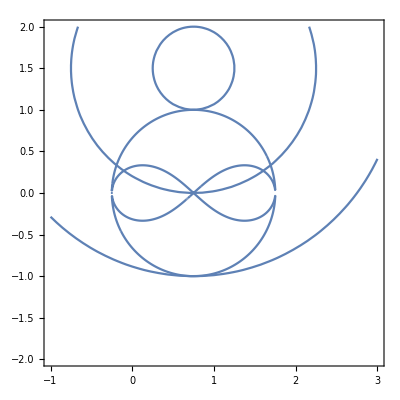

```mathematica
sh1 = Show[ContourPlot[(cir/.r->1.5)==0, {x, -1, 3}, {y, -2, 2}], ContourPlot[(cir/.r->2.5)==0, {x, -1, 3}, {y, -2, 2}], ContourPlot[(cir/.r->0.5)==0, {x, -1, 3}, {y, -2, 2}], plteq3]
```

```mathematica
(*Plotting the solutions from just the second factor only*)
```

```mathematica
pts2 = DeleteDuplicates[{x, y}/.sol2/.sample]
```

{{-0.25,0},{-0.25,0.-1.80278 ⅈ},{-0.25,0.+1.80278 ⅈ},{-0.25,0.},{1.75,0},{1.75,0.-1.80278 ⅈ},{1.75,0.+1.80278 ⅈ},{1.75,0.}}

```mathematica
pts2r = Delete[pts2,List/@{2, 3, 6, 7}]
```

{{-0.25,0},{-0.25,0.},{1.75,0},{1.75,0.}}

```mathematica
(pts2r - ConstantArray[c,Dimensions[pts2r][[1]]])
```

{{-1.,-1.5},{-1.,-1.5},{1.,-1.5},{1.,-1.5}}

```mathematica
Norm[(pts2r - ConstantArray[c,Dimensions[pts2r][[1]]])[[1]]]
```

1.80278

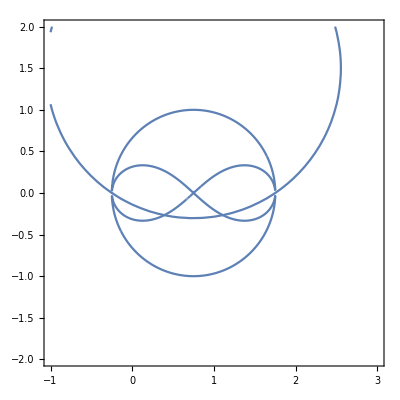

```mathematica
sh2 = Show[ContourPlot[(cir/.r->(Norm[(pts2r - ConstantArray[c,Dimensions[pts2r][[1]]])[[1]]]))==0, {x, -1, 3}, {y, -2, 2}], plteq3]
```

```mathematica
xvals = DeleteDuplicates[Solve[(sy1f[[5]]/.sample)==0, x]]
```

{{x→-0.25},{x→-0.0466919},{x→0.316982},{x→1.18302},{x→1.54669},{x→1.75}}

```mathematica
DeleteDuplicates[NSolve[(sy1f[[5]]/.sample)==0, x]]
```

{{x→-0.25},{x→-0.0466919},{x→0.316982},{x→1.18302},{x→1.54669},{x→1.75}}

```mathematica
DeleteDuplicates[Solve[(eq3/.sample/.xvals[[1]])==0, y]]
```

{{y→0.},{y→0.+1.80278 ⅈ},{y→0.-1.80278 ⅈ}}

```mathematica
(*x, y, being 0, -0.25 was already covered in the above factors*)
```

```mathematica
xytemp = Outer[List, xvals[[2]],Flatten[DeleteDuplicates[Solve[(eq3/.sample/.xvals[[2]])==0, y]]]][[1]]
```

{{x→-0.0466919,y→-0.604386},{x→-0.0466919,y→-0.298142},{x→-0.0466919,y→0.-1.61503 ⅈ},{x→-0.0466919,y→0.+1.61503 ⅈ},{x→-0.0466919,y→0.298142},{x→-0.0466919,y→0.604386}}

```mathematica
Delete[{x, y}/.xytemp, List/@{3, 4}]
```

{{-0.0466919,-0.604386},{-0.0466919,-0.298142},{-0.0466919,0.298142},{-0.0466919,0.604386}}

```mathematica
xytemp = Delete[{x, y}/.xytemp, List/@{3, 4}]-ConstantArray[c, Dimensions[Delete[{x, y}/.xytemp, List/@{3, 4}]][[1]]]
```

{{-0.796692,-2.10439},{-0.796692,-1.79814},{-0.796692,-1.20186},{-0.796692,-0.895614}}

```mathematica
Norm[xytemp[[1]]]
```

2.25015

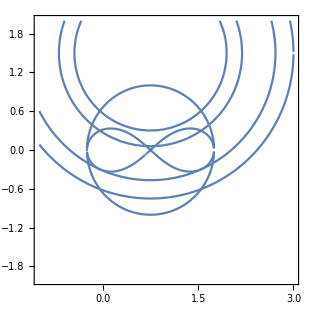

```mathematica
sh3 = Show[ContourPlot[(cir/.r->Norm[xytemp[[1]]])==0, {x, -1, 3}, {y, -2, 2}], ContourPlot[(cir/.r->Norm[xytemp[[2]]])==0, {x, -1, 3}, {y, -2, 2}], ContourPlot[(cir/.r->Norm[xytemp[[3]]])==0, {x, -1, 3}, {y, -2, 2}], ContourPlot[(cir/.r->Norm[xytemp[[4]]])==0, {x, -1, 3}, {y, -2, 2}], plteq3]
```

```mathematica
(*Those roots corresponding the arbit circles also satisfy both the curves*)
```

```mathematica
Chop[eq3/.sample/.xytemp]
```

ReplaceAll::reps: {-0.796692,-2.10439} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-0.796692,-1.79814} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-0.796692,-1.20186} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{0.430664+1.80469 x-4.01563 x^2-9.75 x^3+25.75 x^4-18. x^5+4 x^6-5.14063 y^2-9.75 x y^2+33.5 x^2 y^2-36. x^3 y^2+12 x^4 y^2+7.75 y^4-18. x y^4+12 x^2 y^4+4 y^6/.{-0.796692,-2.10439},0.430664+1.80469 x-4.01563 x^2-9.75 x^3+25.75 x^4-18. x^5+4 x^6-5.14063 y^2-9.75 x y^2+33.5 x^2 y^2-36. x^3 y^2+12 x^4 y^2+7.75 y^4-18. x y^4+12 x^2 y^4+4 y^6/.{-0.796692,-1.79814},0.430664+1.80469 x-4.01563 x^2-9.75 x^3+25.75 x^4-18. x^5+4 x^6-5.14063 y^2-9.75 x y^2+33.5 x^2 y^2-36. x^3 y^2+12 x^4 y^2+7.75 y^4-18. x y^4+12 x^2 y^4+4 y^6/.{-0.796692,-1.20186},0.430664+1.80469 x-4.01563 x^2-9.75 x^3+25.75 x^4-18. x^5+4 x^6-5.14063 y^2-9.75 x y^2+33.5 x^2 y^2-36. x^3 y^2+12 x^4 y^2+7.75 y^4-18. x y^4+12 x^2 y^4+4 y^6/.{-0.796692,-0.895614}}

```mathematica
Chop[sy1f/.sample/.xytemp]
```

ReplaceAll::reps: {-0.796692,-2.10439} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-0.796692,-1.79814} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-0.796692,-1.20186} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{-5.0625 (1.5-2 x)^6 (7/16+1.5 x-x^2)^2 (-2.47928×10^6-5.85793×10^7 x-6.92158×10^7 x^2+1.06807×10^9 x^3+5.25837×10^8 x^4-5.22539×10^9 x^5+6.18332×10^9 x^6-2.86978×10^9 x^7+4.78297×10^8 x^8)/.{-0.796692,-2.10439},-5.0625 (1.5-2 x)^6 (7/16+1.5 x-x^2)^2 (-2.47928×10^6-5.85793×10^7 x-6.92158×10^7 x^2+1.06807×10^9 x^3+5.25837×10^8 x^4-5.22539×10^9 x^5+6.18332×10^9 x^6-2.86978×10^9 x^7+4.78297×10^8 x^8)/.{-0.796692,-1.79814},-5.0625 (1.5-2 x)^6 (7/16+1.5 x-x^2)^2 (-2.47928×10^6-5.85793×10^7 x-6.92158×10^7 x^2+1.06807×10^9 x^3+5.25837×10^8 x^4-5.22539×10^9 x^5+6.18332×10^9 x^6-2.86978×10^9 x^7+4.78297×10^8 x^8)/.{-0.796692,-1.20186},-5.0625 (1.5-2 x)^6 (7/16+1.5 x-x^2)^2 (-2.47928×10^6-5.85793×10^7 x-6.92158×10^7 x^2+1.06807×10^9 x^3+5.25837×10^8 x^4-5.22539×10^9 x^5+6.18332×10^9 x^6-2.86978×10^9 x^7+4.78297×10^8 x^8)/.{-0.796692,-0.895614}}

```mathematica
xytemp = Outer[List, xvals[[3]],Flatten[DeleteDuplicates[Solve[(eq3/.sample/.xvals[[3]])==0, y]]]][[1]]
```

{{x→0.316982,y→-0.901385},{x→0.316982,y→-0.298142},{x→0.316982,y→0.-1.30916 ⅈ},{x→0.316982,y→0.+1.30916 ⅈ},{x→0.316982,y→0.298142},{x→0.316982,y→0.901385}}

```mathematica
Delete[{x, y}/.xytemp, List/@{3, 4}]
```

{{0.316982,-0.901385},{0.316982,-0.298142},{0.316982,0.298142},{0.316982,0.901385}}

```mathematica
xytemp = Delete[{x, y}/.xytemp, List/@{3, 4}]-ConstantArray[c, Dimensions[Delete[{x, y}/.xytemp, List/@{3, 4}]][[1]]]
```

{{-0.433018,-2.40139},{-0.433018,-1.79814},{-0.433018,-1.20186},{-0.433018,-0.598615}}

```mathematica
{
,{-0.43301768250399675,-1.798142396999972},{-0.43301768250399675,-1.201857603000028},{-0.43301768250399675,-0.5986145737594446}}
```

{Null,{-0.433018,-1.79814},{-0.433018,-1.20186},{-0.433018,-0.598615}}

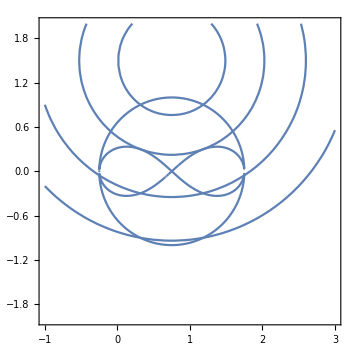

```mathematica
sh4 = Show[ContourPlot[(cir/.r->Norm[xytemp[[1]]])==0, {x, -1, 3}, {y, -2, 2}], ContourPlot[(cir/.r->Norm[xytemp[[2]]])==0, {x, -1, 3}, {y, -2, 2}], ContourPlot[(cir/.r->Norm[xytemp[[3]]])==0, {x, -1, 3}, {y, -2, 2}], ContourPlot[(cir/.r->Norm[xytemp[[4]]])==0, {x, -1, 3}, {y, -2, 2}], plteq3]
```

```mathematica
(*I again get 3 arbit circles not being seen as tangents at all*)
```

```mathematica
xytemp = Outer[List, xvals[[4]],Flatten[DeleteDuplicates[Solve[(eq3/.sample/.xvals[[4]])==0, y]]]][[1]]
```

{{x→1.18302,y→-0.901385},{x→1.18302,y→-0.298142},{x→1.18302,y→0.-1.30916 ⅈ},{x→1.18302,y→0.+1.30916 ⅈ},{x→1.18302,y→0.298142},{x→1.18302,y→0.901385}}

```mathematica
Delete[{x, y}/.xytemp, List/@{3, 4}]
```

{{1.18302,-0.901385},{1.18302,-0.298142},{1.18302,0.298142},{1.18302,0.901385}}

```mathematica
xytemp = Delete[{x, y}/.xytemp, List/@{3, 4}]-ConstantArray[c, Dimensions[Delete[{x, y}/.xytemp, List/@{3, 4}]][[1]]]
```

{{0.433018,-2.40139},{0.433018,-1.79814},{0.433018,-1.20186},{0.433018,-0.598615}}

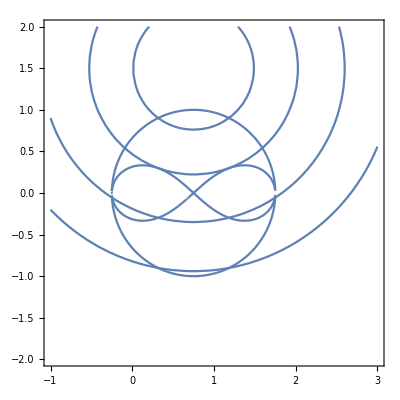

```mathematica
sh5 = Show[ContourPlot[(cir/.r->Norm[xytemp[[1]]])==0, {x, -1, 3}, {y, -2, 2}], ContourPlot[(cir/.r->Norm[xytemp[[2]]])==0, {x, -1, 3}, {y, -2, 2}], ContourPlot[(cir/.r->Norm[xytemp[[3]]])==0, {x, -1, 3}, {y, -2, 2}], ContourPlot[(cir/.r->Norm[xytemp[[4]]])==0, {x, -1, 3}, {y, -2, 2}], plteq3]
```

```mathematica
(*Exactly the same circles as the previous case!*)
```

```mathematica
xytemp = Outer[List, xvals[[5]],Flatten[DeleteDuplicates[Solve[(eq3/.sample/.xvals[[5]])==0, y]]]][[1]]
```

{{x→1.54669,y→-0.604386},{x→1.54669,y→-0.298142},{x→1.54669,y→0.-1.61503 ⅈ},{x→1.54669,y→0.+1.61503 ⅈ},{x→1.54669,y→0.298142},{x→1.54669,y→0.604386}}

```mathematica
Delete[{x, y}/.xytemp, List/@{3, 4}]
```

{{1.54669,-0.604386},{1.54669,-0.298142},{1.54669,0.298142},{1.54669,0.604386}}

```mathematica
xytemp = Delete[{x, y}/.xytemp, List/@{3, 4}]-ConstantArray[c, Dimensions[Delete[{x, y}/.xytemp, List/@{3, 4}]][[1]]]
```

{{0.796692,-2.10439},{0.796692,-1.79814},{0.796692,-1.20186},{0.796692,-0.895614}}

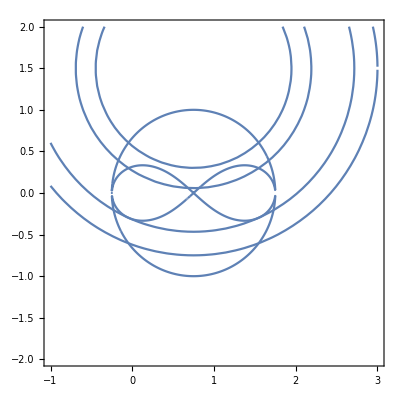

```mathematica
sh6 = Show[ContourPlot[(cir/.r->Norm[xytemp[[1]]])==0, {x, -1, 3}, {y, -2, 2}], ContourPlot[(cir/.r->Norm[xytemp[[2]]])==0, {x, -1, 3}, {y, -2, 2}], ContourPlot[(cir/.r->Norm[xytemp[[3]]])==0, {x, -1, 3}, {y, -2, 2}], ContourPlot[(cir/.r->Norm[xytemp[[4]]])==0, {x, -1, 3}, {y, -2, 2}], plteq3]
```

```mathematica
(*Same as previous but one case*)
```

```mathematica
xytemp = Outer[List, xvals[[5]],Flatten[DeleteDuplicates[Solve[(eq3/.sample/.xvals[[5]])==0, y]]]][[1]]
```

{{x→1.54669,y→-0.604386},{x→1.54669,y→-0.298142},{x→1.54669,y→0.-1.61503 ⅈ},{x→1.54669,y→0.+1.61503 ⅈ},{x→1.54669,y→0.298142},{x→1.54669,y→0.604386}}

```mathematica
Delete[{x, y}/.xytemp, List/@{3, 4}]
```

{{1.54669,-0.604386},{1.54669,-0.298142},{1.54669,0.298142},{1.54669,0.604386}}

```mathematica
xytemp = Delete[{x, y}/.xytemp, List/@{3, 4}]-ConstantArray[c, Dimensions[Delete[{x, y}/.xytemp, List/@{3, 4}]][[1]]]
```

{{0.796692,-2.10439},{0.796692,-1.79814},{0.796692,-1.20186},{0.796692,-0.895614}}

```mathematica
sh7 = Show[ContourPlot[(cir/.r->Norm[xytemp[[1]]])==0, {x, -1, 3}, {y, -2, 2}], ContourPlot[(cir/.r->Norm[xytemp[[2]]])==0, {x, -1, 3}, {y, -2, 2}], ContourPlot[(cir/.r->Norm[xytemp[[3]]])==0, {x, -1, 3}, {y, -2, 2}], ContourPlot[(cir/.r->Norm[xytemp[[4]]])==0, {x, -1, 3}, {y, -2, 2}], plteq3]
```

-Graphics-

```mathematica
(*Again the circles represent one of the above circles*)
```

```mathematica
xytemp = Outer[List, xvals[[6]],Flatten[DeleteDuplicates[Solve[(eq3/.sample/.xvals[[6]])==0, y]]]][[1]]
```

{{x→1.75,y→-0.000108117-0.000108118 ⅈ},{x→1.75,y→-0.000108117+0.000108118 ⅈ},{x→1.75,y→0.-1.80278 ⅈ},{x→1.75,y→0.+1.80278 ⅈ},{x→1.75,y→0.000108117-0.000108118 ⅈ},{x→1.75,y→0.000108117+0.000108118 ⅈ}}

```mathematica
(*It has all imaginary roots. But a few close to zero represent the same solutions plotted previously*)
```

```mathematica
(*These are all the solutions we have except that we have 6 arbit circles!*)
```

```mathematica
D[eq3, x]/.{x-> 1.5466918531409661,y-> -0.6043857138771703}/.sample
```

5.23831

```mathematica
D[eq3, y]/.{x-> 1.5466918531409661,y-> -0.6043857138771703}/.sample
```

-3.97388

```mathematica
(*The solution correspoding to these equations are not double points hence cannot be any of the acnodes, crunodes or cusps*)
```

```mathematica
Show[sh1, sh2, sh3, sh4, sh5, sh6, sh7]
```

-Graphics-

```mathematica
sample
```

{l0→1.5,l1→1,r1→3/4,k→1.5}

```mathematica
genc = (x-h)^2+(y-k)^2-r^2
```

-r^2+(-h+x)^2+(-k+y)^2

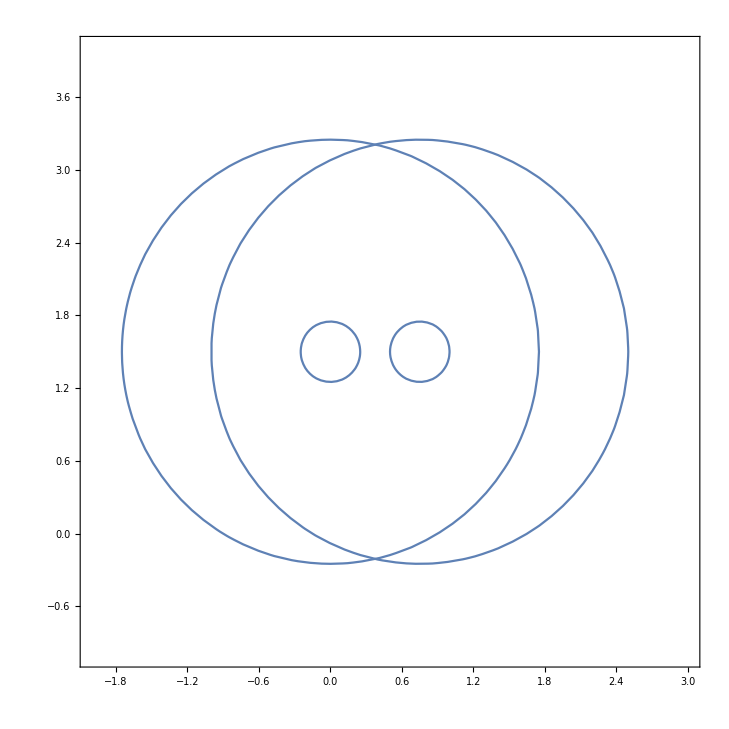

```mathematica
Show[ContourPlot[(genc/.{h->0, g->0, r->l1+r1}/.sample)==0, {x, -2, 3}, {y, -1, 4}], ContourPlot[(genc/.{h->0, g->0, r->Abs[l1-r1]}/.sample)==0,{x, -2, 3}, {y, -1, 4}], ContourPlot[(genc/.{h->l0/2, g->0, r->l1+r1}/.sample)==0, {x, -2, 3}, {y, -1, 4}], ContourPlot[(genc/.{h->l0/2, g->0, r->Abs[l1-r1]}/.sample)==0, {x, -2, 3}, {y, -1, 4}]]
```

```mathematica
(*Still need to verify the radius deifinition between the FSM circles and the worspace circles.*)
```

```mathematica
(*Cheking if these solutions corresponding to the arbit circles satisfy both the univariate and the singularity curve*)
```

```mathematica
eq3/.{x-> -0.04669185314090546,y-> -0.6043857138772473}/.sample
```

-4.44089×10^-16

```mathematica
sy1f/.{x-> -0.04669185314090546,y-> -0.6043857138772473}/.sample
```

-3.70635×10^-7

```mathematica
eq3/.{x-> 1.5466918531409661,y-> -0.6043857138771703}/.sample
```

3.01981×10^-14

```mathematica
sy1f/.sample/.{x-> 1.5466918531409661,y-> -0.6043857138771703}
```

0.000179223

```mathematica
eq3/.{x->1.5466918531409661,y->-0.298142396999938}/.sample
```

3.55271×10^-14

```mathematica
sy1f/.{x->1.5466918531409661,y->-0.298142396999938}/.sample
```

0.000237207

```mathematica
(*These points even satisfy the curves. I dont understand how I get these points. So checking if they satisfy the tangency condition tc1 also*)
```

```mathematica
tc1/.h->l0/2/.{x->1.5466918531409661,y->-0.298142396999938}/.sample
```

-2.20268×10^-13

```mathematica
tc1/.h->l0/2/.sample/.{x-> 1.5466918531409661,y-> -0.6043857138771703}
```

3.92873

```mathematica
tc1/.h->l0/2/.{x-> -0.04669185314090546,y-> -0.6043857138772473}/.sample
```

-3.92873

```mathematica
tc1/.h->l0/2/.sample/.{x->1.5466918531409661,y->-0.6043857138771703}
```

3.92873

```mathematica
tc1/.h->l0/2/.sample/.{x->1.5466918531409661,y->-0.298142396999938}
```

-2.71783×10^-13

```mathematica
tc1/.h->l0/2/.sample/.{x->1.5466918531409661,y->0.6043857138771704}
```

3.92873

```mathematica
tc1/.h->l0/2/.sample/.{x->1.5466918531409661,y->0.298142396999938}
```

-1.18172

```mathematica
tc2 =tc1/.h->l0/2
```

k l0^3 l1^2-2 k l0 l1^4-k l0^3 r1^2+4 k l0 l1^2 r1^2-2 k l0 r1^4+k l0^4 x-10 k l0^2 l1^2 x+4 k l1^4 x+10 k l0^2 r1^2 x-8 k l1^2 r1^2 x+4 k r1^4 x-9 k l0^3 x^2+24 k l0 l1^2 x^2-24 k l0 r1^2 x^2+26 k l0^2 x^3-16 k l1^2 x^3+16 k r1^2 x^3-30 k l0 x^4+12 k x^5-(l0^5 y)/2+2 l0^3 l1^2 y+3 l0^4 x y-4 l0^2 l1^2 x y-6 l0^3 x^2 y+4 l0^2 x^3 y-3 k l0^3 y^2+8 k l0 l1^2 y^2-8 k l0 r1^2 y^2+18 k l0^2 x y^2-16 k l1^2 x y^2+16 k r1^2 x y^2-36 k l0 x^2 y^2+24 k x^3 y^2-2 l0^3 y^3+4 l0^2 x y^3-6 k l0 y^4+12 k x y^4

```mathematica
sylnew = ResidualSylv[tc2, eq3, y]
```

{(l0/2-x)^6 (2 (1) ((l0^2 l1^4-2 l0^2 l1^2 r1^2+l0^2 r1^4+2 l0^3 l1^2 x-4 l0 l1^4 x-2 l0^3 r1^2 x+8 l0 l1^2 r1^2 x-4 l0 r1^4 x+l0^4 x^2-10 l0^2 l1^2 x^2+4 l1^4 x^2+10 l0^2 r1^2 x^2-8 l1^2 r1^2 x^2+4 r1^4 x^2-6 l0^3 x^3+16 l0 l1^2 x^3-16 l0 r1^2 x^3+13 l0^2 x^4-8 l1^2 x^4+8 r1^2 x^4-12 l0 x^5+4 x^6) (-4 (-(-l0^4+4 l0^2 l1^2+4 l0^3 x-4 l0^2 x^2) ((-29376 k^3 l0^6+3840 k l0^8+103680 k^3 l0^4 l1^2-4096 k l0^6 l1^2-86016 k^3 l0^2 l1^4-152064 k^3 l0^4 r1^2+12+9216 k l0^6 x^2+285696 k^3 l0^2 l1^2 x^2-423936 k^3 l0^2 r1^2 x^2+497664 k^3 l0^3 x^3-248832 k^3 l0^2 x^4) (31+4 x^6)-1+(1) 1)-1+1)+1)-1)-1),{1}}
 |  |  |  |

```mathematica
sylnewf = Factor[sylnew][[1]];
```

```mathematica
xsolnew = DeleteDuplicates[Solve[(sylnewf[[5]]/.sample)==0, x]]
```

{{x→-0.25},{x→-0.0466919},{x→0.316982},{x→1.18302},{x→1.54669},{x→1.75}}

```mathematica
temptc = tc2/.xsolnew/.sample
```

{0.-25.5 y^2-9. y^3-18. y^4,1.57875+2.61916 y-9.83902 y^2-7.17023 y^3-14.3405 y^4,-0.923513+3.16642 y+1.62375 y^2-3.89716 y^3-7.79432 y^4,0.923513-3.16642 y-1.62375 y^2+3.89716 y^3+7.79432 y^4,-1.57875-2.61916 y+9.83902 y^2+7.17023 y^3+14.3405 y^4,2.11209×10^-12+1.49214×10^-12 y+25.5 y^2+9. y^3+18. y^4}

```mathematica
sols/.sample
```

{{x→0.75,y→0},{x→0.75,y→0.-1.11803 ⅈ},{x→0.75,y→0.+1.11803 ⅈ},{x→0.75,y→-1.},{x→0.75,y→1.},{x→-0.25,y→0},{x→-0.25,y→0.-1.80278 ⅈ},{x→-0.25,y→0.+1.80278 ⅈ},{x→-0.25,y→0.},{x→-0.25,y→0.},{x→1.75,y→0},{x→1.75,y→0.-1.80278 ⅈ},{x→1.75,y→0.+1.80278 ⅈ},{x→1.75,y→0.},{x→1.75,y→0.}}

```mathematica
Solve[temptc[[1]]==0, y]
```

{{y→-0.25-1.16369 ⅈ},{y→-0.25+1.16369 ⅈ},{y→0.},{y→0.}}

```mathematica
(*These solutions {-0.25, 0} are already covered in the above solutions*)
```

```mathematica
Solve[temptc[[2]]==0, y]
```

{{y→-0.309669-0.888024 ⅈ},{y→-0.309669+0.888024 ⅈ},{y→-0.298142},{y→0.417481}}

```mathematica
tc1/.{x->-0.04669185314090546, y->-0.29814239699997197}/.h->l0/2/.sample
```

-6.66134×10^-16

```mathematica
eq3/.h->l0/2/.sample/.{x->-0.04669185314090546, y->-0.29814239699997197}
```

-2.77556×10^-17

```mathematica
Norm[({x, y}/.{x->-0.04669185314090546, y->-0.29814239699997197})-c]
```

1.96673

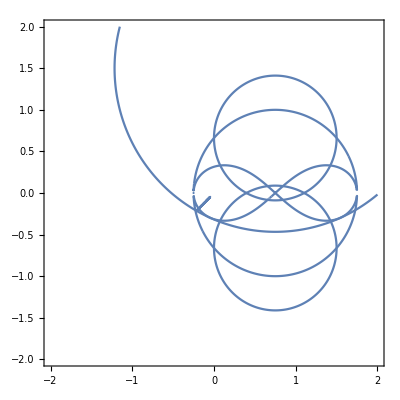

```mathematica
Show[ContourPlot[(cir/.r->Norm[({x, y}/.{x->-0.04669185314090546, y->-0.29814239699997197})-c])==0, {x, -2, 2}, {y, -2, 2}, PlotPoints->100, MaxRecursion->3], plteq3, plteq4]
```

```mathematica
tc1/.h->l0/2/.sample/.{x->-0.04669185314090546, y->0.41748088046782106}
```

0.

```mathematica
eq3/.sample/.{x->-0.04669185314090546, y->0.41748088046782106}
```

-0.181549

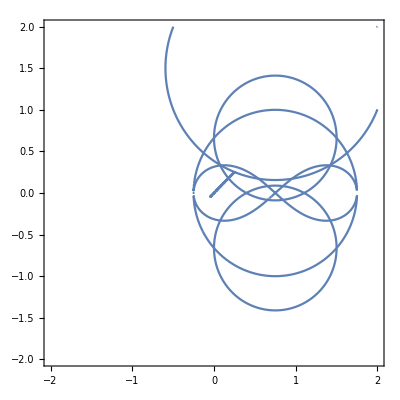

```mathematica
Show[ContourPlot[(cir/.r->Norm[({x, y}/.{x->-0.04669185314090546, y->0.41748088046782106})-c])==0, {x, -2, 2}, {y, -2, 2}, PlotPoints->100, MaxRecursion->3], plteq3, plteq4]
```

```mathematica
Solve[temptc[[3]]==0, y]
```

{{y→-0.666565-0.546383 ⅈ},{y→-0.666565+0.546383 ⅈ},{y→0.298142},{y→0.534988}}

```mathematica
(*Same as the above case the eq3 doesnt satisfy this point*)
```

```mathematica
eq3/.sample/.{x->0.31698231749600325,y->0.5349877566889426}
```

-0.830829

```mathematica
tc1/.h->l0/2/.sample/.{x->0.31698231749600325,y->0.29814239699997186}
```

-4.996×10^-16

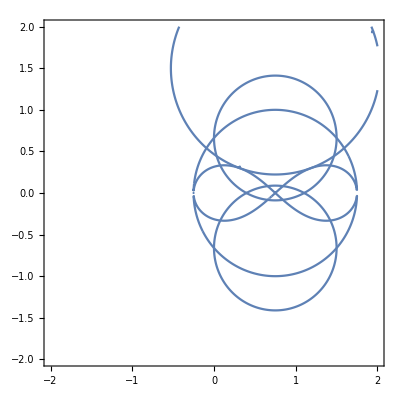

```mathematica
Show[ContourPlot[(cir/.r->Norm[({x, y}/.{x->0.31698231749600325,y->0.29814239699997186})-c])==0, {x, -2, 2}, {y, -2, 2}, PlotPoints->100, MaxRecursion->3], plteq3, plteq4]
```

```mathematica
eq3/.{xsolnew[[4]][[1]], y->0.5349877566889425}/.sample
```

-0.830829

```mathematica
Solve[temptc[[4]]==0, y]
```

{{y→-0.666565-0.546383 ⅈ},{y→-0.666565+0.546383 ⅈ},{y→0.298142},{y→0.534988}}

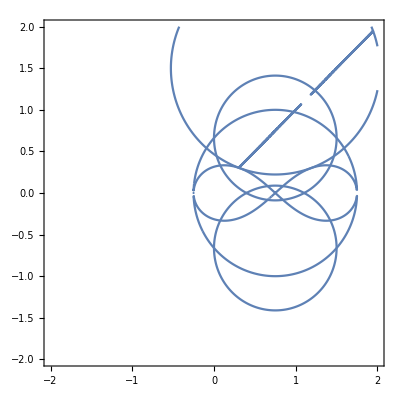

```mathematica
Show[ContourPlot[(cir/.r->Norm[({x, y}/.{xsolnew[[4]][[1]], y->0.29814239699997913})-c])==0, {x, -2, 2}, {y, -2, 2}, PlotPoints->100, MaxRecursion->3], plteq3, plteq4]
```

```mathematica
eq3/.{xsolnew[[5]][[1]], y->-0.2981423969999656}/.sample
```

-3.55271×10^-14

```mathematica
Solve[temptc[[5]]==0, y]
```

{{y→-0.309669-0.888024 ⅈ},{y→-0.309669+0.888024 ⅈ},{y→-0.298142},{y→0.417481}}

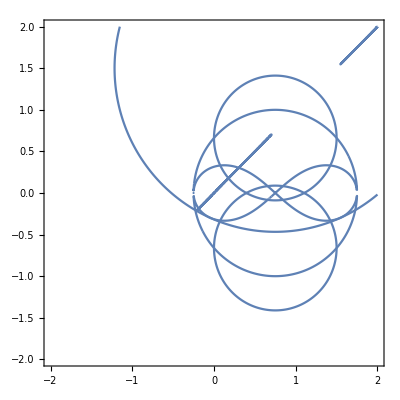

```mathematica
Show[ContourPlot[(cir/.r->Norm[({x, y}/.{xsolnew[[5]][[1]], y->-0.2981423969999656})-c])==0, {x, -2, 2}, {y, -2, 2}, PlotPoints->100, MaxRecursion->3], plteq3, plteq4]
```

```mathematica
Chop[Solve[temptc[[6]]==0, y]]
```

{{y→-0.25-1.16369 ⅈ},{y→-0.25+1.16369 ⅈ},{y→0.-2.87797×10^-7 ⅈ},{y→0.+2.87797×10^-7 ⅈ}}

```mathematica
xsolnew[[6]]
```

{x→1.75}

```mathematica
Export["eq3.txt",CForm[eq3/.replist]]
```

eq3.txt

```mathematica
Export["tc2.txt",CForm[tc2/.replist]]
```

tc2.txt

```mathematica
(*Trying to get a linear relation in x, y to get the common roots*)
```

```mathematica
eq3
```

l0^2 l1^4-2 l0^2 l1^2 r1^2+l0^2 r1^4+2 l0^3 l1^2 x-4 l0 l1^4 x-2 l0^3 r1^2 x+8 l0 l1^2 r1^2 x-4 l0 r1^4 x+l0^4 x^2-10 l0^2 l1^2 x^2+4 l1^4 x^2+10 l0^2 r1^2 x^2-8 l1^2 r1^2 x^2+4 r1^4 x^2-6 l0^3 x^3+16 l0 l1^2 x^3-16 l0 r1^2 x^3+13 l0^2 x^4-8 l1^2 x^4+8 r1^2 x^4-12 l0 x^5+4 x^6+l0^4 y^2-6 l0^2 l1^2 y^2+4 l1^4 y^2+2 l0^2 r1^2 y^2-8 l1^2 r1^2 y^2+4 r1^4 y^2-6 l0^3 x y^2+16 l0 l1^2 x y^2-16 l0 r1^2 x y^2+18 l0^2 x^2 y^2-16 l1^2 x^2 y^2+16 r1^2 x^2 y^2-24 l0 x^3 y^2+12 x^4 y^2+5 l0^2 y^4-8 l1^2 y^4+8 r1^2 y^4-12 l0 x y^4+12 x^2 y^4+4 y^6

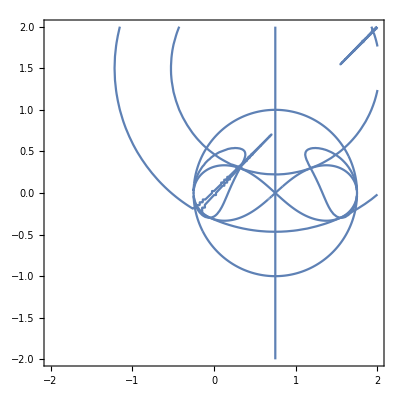

```mathematica
Show[ContourPlot[(tc2/.sample)== 0, {x, -2, 2}, {y, -2, 2}], plteq3, ContourPlot[(cir/.r->Norm[({x, y}/.{x->0.31698231749600325,y->0.29814239699997186})-c])==0, {x, -2, 2}, {y, -2, 2}], ContourPlot[(cir/.r->Norm[({x, y}/.{xsolnew[[5]][[1]], y->-0.2981423969999656})-c])==0, {x, -2, 2}, {y, -2, 2}]]
```

```mathematica
Exponent[tc2,x]
```

5

```mathematica
Exponent[eq3, x]
```

6

```mathematica
rem1 = Simplify[PolynomialRemainder[eq3, tc2, y]];
```

```mathematica
rem2 = Simplify[PolynomialRemainder[tc2, rem1, y]];
```

```mathematica
rem3 = Simplify[PolynomialRemainder[rem1, rem2, y]];
```

```mathematica
remy = Solve[rem3==0, y];
```

```mathematica
remysol = remy/.sample/.xvals//.{x_List}:>x
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{{y→Indeterminate},{y→-0.298142},{y→0.298142},{y→0.298142},{y→-0.298142},{y→-20.6667}}

```mathematica
xvals
```

{{x→-0.25},{x→-0.0466919},{x→0.316982},{x→1.18302},{x→1.54669},{x→1.75}}

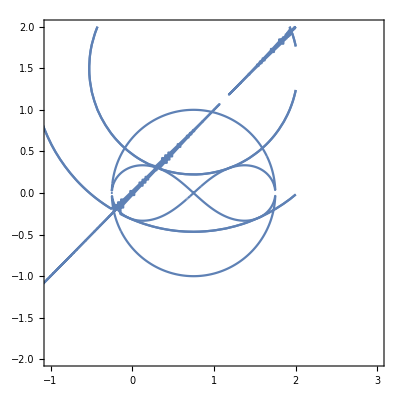

```mathematica
Show[plteq3, ContourPlot[(cir/.r->Norm[({x, y}/.{x->-0.04669185314090546,y->-0.29814239699997175})-c])==0, {x, -2, 2}, {y, -2, 2}], 
 ContourPlot[(cir/.r->Norm[({x, y}/.{x->0.31698231749600325,y->0.2981423969999728})-c])==0, {x, -2, 2}, {y, -2, 2}],  ContourPlot[(cir/.r->Norm[({x, y}/.{x->1.1830176825039926,y->0.2981423969999766})-c])==0, {x, -2, 2}, {y, -2, 2}], 
ContourPlot[(cir/.r->Norm[({x, y}/.{x->1.5466918531409661,y->-0.29814239699975836})-c])==0, {x, -2, 2}, {y, -2, 2}], 
ContourPlot[(cir/.r->Norm[({x, y}/.{x->1.750000000000082,y->-20.666666666666668})-c])==0, {x, -2, 2}, {y, -2, 2}]]
```

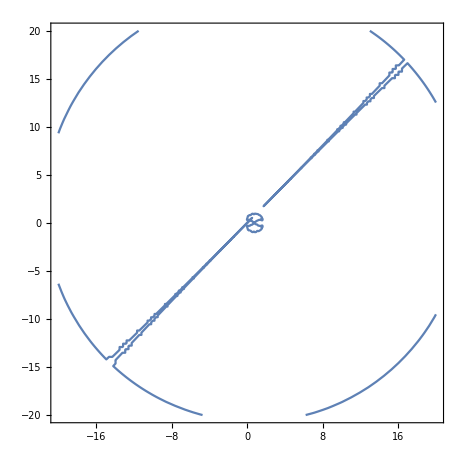

```mathematica
Show[ContourPlot[(eq3/.sample)==0, {x, -20, 20}, {y, -20, 20}], ContourPlot[(cir/.r->Norm[({x, y}/.{x->1.750000000000082,y->-20.666666666666668})-c])==0, {x, -20, 20}, {y, -20, 20}]]
```

```mathematica
(*So even after finding the common root by divinding, I have an arbitrary circle of {1.75, -20}! *)
```

```mathematica
eq3/.sample/.{x->1.750000000000082,y->-20.666666666666668}
```

3.14033×10^8

```mathematica
tempsy1 = Simplify[sy1/.h->l0/2/.sample]
```

2.73649×10^7+6.15291×10^8 x-5.49815×10^8 x^2-2.45391×10^10 x^3+3.31238×10^10 x^4+3.74631×10^11 x^5-1.00751×10^12 x^6-1.71935×10^12 x^7+1.07197×10^13 x^8-1.23087×10^13 x^9-2.21968×10^13 x^10+9.44606×10^13 x^11-1.54849×10^14 x^12+1.53846×10^14 x^13-1.01056×10^14 x^14+4.43803×10^13 x^15-1.25897×10^13 x^16+2.09207×10^12 x^17-1.54968×10^11 x^18

```mathematica
(*Plotting the gain type singularity curves*)
```

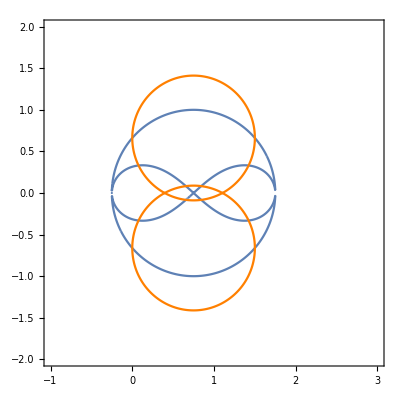

```mathematica
Show[plteq3, plteq4]
```

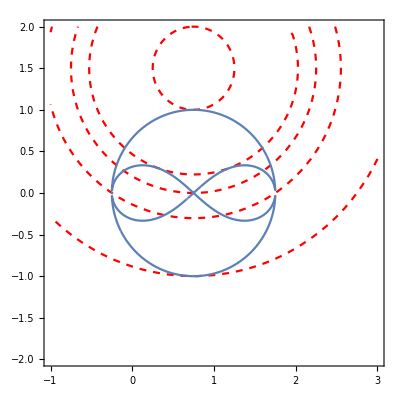

```mathematica
Show[ContourPlot[(cir/.r->Norm[({x, y}/.{x->0.31698231749600325,y->0.29814239699997186})-c])==0, {x, -1, 3}, {y, -2, 2}, PlotPoints->6, MaxRecursion->3, ContourStyle->{Dashed, Red}], 
ContourPlot[(cir/.r->Norm[xytemp[[3]]])==0, {x, -1, 3}, {y, -2, 2}, PlotPoints->6, MaxRecursion->3, ContourStyle->{Dashed, Red}], 
ContourPlot[(cir/.r->(Norm[(pts2r - ConstantArray[c,Dimensions[pts2r][[1]]])[[1]]]))==0, {x, -1, 3}, {y, -2, 2}, PlotPoints->6, MaxRecursion->3, ContourStyle->{Dashed, Red}],
ContourPlot[(cir/.r->1.5)==0, {x, -1, 3}, {y, -2, 2}, PlotPoints->6, MaxRecursion->3, ContourStyle->{Dashed, Red}], ContourPlot[(cir/.r->2.5)==0, {x, -1, 3}, {y, -2, 2}, PlotPoints->6, MaxRecursion->3, ContourStyle->{Dashed, Red}], ContourPlot[(cir/.r->0.5)==0, {x, -1, 3}, {y, -2, 2}, PlotPoints->6, MaxRecursion->3, ContourStyle->{Dashed, Red}],
plteq3]
```